```mathematica
Manipulate[
Module[{r,a,f1,f2,hA,hB,hC,x1hA,x2hA,x1hB,x2hB,x1hC,x2hC,xh,g1,g2,color},
r=6.204;
a=4*r;
f1[x_]=-√(r^2-x^2)+r;
f2[x_]=√(r^2-x^2)+r;
g1[x_]=-√(r^2-x^2-a^2+2*x*a)+r;
g2[x_]=√(r^2-x^2-a^2+2*x*a)+r;

xh[h_]=x/.Quiet@Solve[h==f1[x],x,Reals];
hA=1.5;x1hA=xh[hA][[1]];x2hA=xh[hA][[2]];
hB=0.9;x1hB=xh[hB][[1]];x2hB=xh[hB][[2]];
hC=0.35;x1hC=xh[hC][[1]];x2hC=xh[hC][[2]];

color=If[col==1,Blue,White];

Show[
Graphics[{
(*Line[{{x1hA,hA},{x2hA,hA}}],Line[{{x1hB,hB},{x2hB,hB}}],*)
{PointSize[0.012],RGBColor[0.06,1.,0.26],Point[Table[{x,hA},{x,x1hA,x2hA,0.5}]],Point[Table[{x,hB},{x,x1hB,x2hB,0.5}]],Point[Table[{x,hC},{x,x1hC,x2hC,0.5}]]},
{color,Thickness[0.006],Circle[{0,r},r+0.15]}
}],
Plot[{f1[x],f2[x]},{x,-r,r},PlotStyle->{{Thick,Black},{Thick,Black}}],
Plot[{g1[x],g2[x]},{x,a-r,a+r},PlotStyle->{{Thick,Black},{Thick,Black}}],
AspectRatio->Automatic,ImageSize->{550,350},AxesOrigin->{0,r},Axes->False,PlotRange->{{-r,a+r},{-7.5,16}}
]
],
{{col,2,""},{1->"Blue",2->"White"},Setter}]
```

```mathematica
(*{PointSize[0.012],Point[Table[{x,hA},{x,x1hA+0.5,x2hA-0.5,0.5}]],Point[Table[{x,hB},{x,x1hB+0.5,x2hB-0.5,0.5}]],Point[Table[{x,hC},{x,x1hC+0.5,x2hC-0.5,0.5}]]}*)
```

```mathematica
Manipulate[
Module[{r,a,f1,f2,g1,g2,xA,xB},
r=6.204;
a=4*r;
f1[x_]=-√(r^2-x^2)+r;
f2[x_]=√(r^2-x^2)+r;
g1[x_]=-√(r^2-x^2-a^2+2*x*a)+r;
g2[x_]=√(r^2-x^2-a^2+2*x*a)+r;

(*θ[height_]=ArcSin[(r-height)/r];*)
xA[height_]=r*Cos[-π-ArcSin[(r-height)/r]];
xB[height_]=r*Cos[ArcSin[(r-height)/r]];

Show[
Graphics[{
{Blue,Table[{
PointSize[RandomReal[{0.007,0.015}]],
{Point[{RandomReal[{xA[h],xB[h]}],h}],Point[{RandomReal[{xA[h*2/3],xB[h*2/3]}],h*2/3}],Point[{RandomReal[{xA[h*1/3],xB[h*1/3]}],h*1/3}]}
},{25}]},
{White,Thickness[0.006],Circle[{0,r},r+0.15]}
}],
Plot[{f1[x],f2[x]},{x,-r,r},PlotStyle->{{Thick,Black},{Thick,Black}}],
Plot[{g1[x],g2[x]},{x,a-r,a+r},PlotStyle->{{Thick,Black},{Thick,Black}}],
AspectRatio->Automatic,ImageSize->{550,350},AxesOrigin->{0,r},Axes->False,PlotRange->{{-r,a+r},{-7.5,16}}
]
],
{{h,1.5,""},0.2,1.5,0.1,Appearance->"Labeled"}]
```

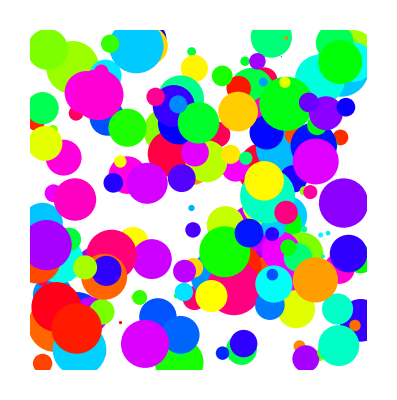

```mathematica
Graphics[Table[{Hue[RandomReal[]],PointSize[RandomReal[{0,0.1}]],Point[RandomReal[1,{2}]]},{200}]]
```